```mathematica
{$Version,Date[]}
```

{11.3.0 for Microsoft Windows (64-bit) (March 7, 2018),{2018,4,25,15,0,9.090734}}

## Examples from ComplexPlot.m

```mathematica
(* Turn off error messages *)
msgonindet = Head[General::"indet"]=!=$Off;
Off[Arg::"indet" ];
```

```mathematica
QComplexDensityPlot[x+I y, {x,-4,4}, {y,-4,4}]
```

-Graphics-

```mathematica
gr1=QComplexDensityPlot[Sin[x + I y],
        {x,-Pi,Pi}, {y,-1,2.5},
        Mesh->False, PlotPoints->30]
```

-Graphics-

(* There is a problem here in 6 ... : gr1 is already Graphics[Raster[]]
Probably need another function for this example:
Show[SurfaceGraphics[gr1],
    AspectRatio->Automatic,Axes->True,Mesh->True]
*)

```mathematica
QComplexContourPlot[x + I y, {x,-4,4}, {y,-4,4},
    QValueRange->{2,5},
    PlotRange->{0,3},Contours->5,
    ContourStyle->GrayLevel[0.5]]
```

-Graphics-

```mathematica
QComplexContourPlot[Zeta[x + I y],
    {x,-.7,2.5}, {y,-2,42},
    PlotPoints->{10,50}, PlotRange->{-1.5,8},
    Contours->8, AspectRatio->5,ImageSize->150]
```

-Graphics-

```mathematica
myfunc[{y_,m_,c_}] := Hue[-2 y,1-m,c];
collist=Table[myfunc[Mod[{x,x+y,x-y},1]],
        {y,0,1,1/20.}, {x,0,1,1/20.}];
QColorArrayPlot[collist,Mesh->False]
```

-Graphics-

```mathematica
lis = Table[N[Tan[x + I y]],
        {y,-1.,1,.1},{x,-N[Pi],Pi,N[Pi]/10}];
QListComplexDensityPlot[lis,
    MeshRange->{{-Pi,Pi},{-1,1}}]
```

-Graphics-

```mathematica
QComplexPlot3D[2 Exp[-x^2 - y^2 - 3 I x] Sin[x + I y],
    {x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
f[x_,y_]:=
   Which[Abs[x+I y] > 1.1, Indeterminate,
		Abs[x+I y] > 0.8, 0,
		Abs[x+I y] > 0.5, ComplexInfinity,
		True, DirectedInfinity[x+I y]];

QComplexDensityPlot[f[x,y],{x,-1,1},{y,-1,1},Compiled->False,
    QLightnessRange->{.2,.8}]
```

-Graphics-

```mathematica
QComplexDensityPlot[f[x,y],{x,-1,1},{y,-1,1},QValueChecking->Off,
    Compiled->False,QLightnessRange->{.2,.8}]
```

-Graphics-

```mathematica
arr = Table[Exp[I 3 (x+y) - x^2-y^2] +
            Exp[-I 2 (x+y) - (x-.5)^2-(y-.5)^2],
               {y,-3,3,.1},{x,-3,3,.1}];
QListComplexSurfacePlot[arr,PlotRange->All,
 QSphereRadius->0.5,
MaxPlotPoints->30,
    QLightnessRange->{0.2,1.}]
```

-Graphics3D-

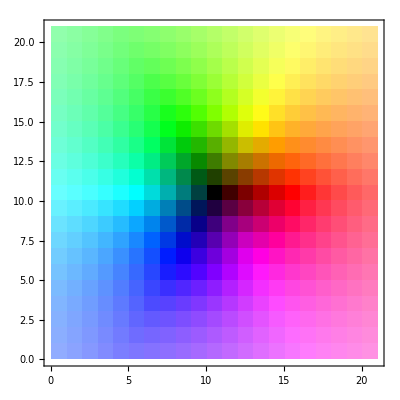

```mathematica
QColorArrayPlot[
	Table[QComplexToRGBColor[x + I y], {y,-2.,2,.2}, {x,-2.,2,.2}],
        Mesh->False]
```

```mathematica
QSpinorDensityPlot[{Exp[I x],Exp[I y]}, {x,-Pi,Pi}, {y,-Pi,Pi}, 
	PlotPoints->20]
```

-Graphics-